```mathematica
SetDirectory@NotebookDirectory[];
Import["Qubits_package.m"];
Import["ExactKrylov_package.m"];
```

## Parameters

```mathematica
Nq=10;
(*HamType="Heisenberg";*)
HamType="FermiHubbard";
(*GraphType="Chain";*)
GraphType="Ladder";
```

```mathematica
logηList=Table[-0.1*j,{j,-50,150}];
PR={{1.*^-3,1.*^12},{1.*^-14,1.*^1}};
```

## Model

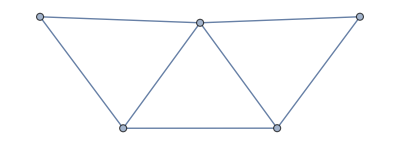

```mathematica
If[StringMatchQ[HamType,"Heisenberg"],(
EL=funGraph[Nq,GraphType];
Model=funHeisenberg[Nq,EL]
)];
If[StringMatchQ[HamType,"FermiHubbard"],(
EL=funGraph[Nq/2,GraphType];
u=1.;
Model=funFermiHubbard[Nq,EL,u]
)];
Graph[EL]
```

```mathematica
Ham=funHamiltonianQubit[Model];
```

## Spectrum

```mathematica
{EE,ES}=funSpectrum[Ham];
HamNorm=Max[Abs[EE]];
EE=EE/HamNorm;
Eg=EE[[1]]
```

-0.721501

```mathematica
If[StringMatchQ[HamType,"Heisenberg"],(
htot=3.*Length[EL]/HamNorm
)]
If[StringMatchQ[HamType,"FermiHubbard"],(
htot=(2.*Length[EL]+u/4.*Nq/2.)/HamNorm
)]
```

1.17428

## Reference state

```mathematica
If[StringMatchQ[HamType,"Heisenberg"],(
ψ=funPairwiseSinglet[Nq]
)];
If[StringMatchQ[HamType,"FermiHubbard"],(
ψ=funHartreeFock[Nq,EL]
)];
ψ=Conjugate[ES].ψ;
ψ=Flatten[ψ];
Proψ=Abs[ψ]^2;
```

```mathematica
pg=Proψ[[1]]
ER=Total[Proψ*EE];
ϵR=ER-Eg
```

0.60369

0.0223459

## Run

```mathematica
dList=Table[d,{d,2,30}];
plotsRTE={};
plotsF={};
plots={};
γ2ϵK={};
```

```mathematica
Do[(
d=dList[[l]];
Ide=IdentityMatrix[d];

E0=Eg+1.;
{Hmat,Smat}=funMatPower[EE,Proψ,d,E0];
EB=Hmat[[d,d]]/Smat[[d,d]];
ϵB=EB-Eg;
logη=-15;
η=10.^logη;
{EK,cn}=funDiagonalisation[Hmat+2.*η*Ide,Smat+2.*η*Ide];
ϵK=EK-Eg;
If[ϵK>1.*^-2||ϵK<1.*^-9,(
Print[{d,ϵK}];
Goto[end];
)];
{γList,ϵList}=funGammaEpsilon[Eg,pg,Hmat,Smat,Ide,1.,1.,logηList];
γListP=γList;
ϵListP=ϵList;
ϵMin=Min[ϵList];
If[ϵMin<2.*ϵK,(
γ=funInterpolation[ϵList,γList,2.*ϵK];
),(
γ=0.;
)];
γP=γ;

E0=0;
{Hmat,Smat}=funMatChebyshev[EE,Proψ,d,htot,E0];
{γList,ϵList}=funGammaEpsilon[Eg,pg,Hmat,Smat,Ide,1.,1.,logηList];
γListCP=γList;
ϵListCP=ϵList;
ϵMin=Min[ϵList];
If[ϵMin<2.*ϵK,(
γ=funInterpolation[ϵList,γList,2.*ϵK];
),(
γ=0.;
)];
γCP=γ;

E0=Eg;
τMIN=0;
τMAX=64;
Do[(
τ=(τMIN+τMAX)/2.;
{Hmat,Smat}=funMatGaussianPower[EE,Proψ,1,htot,τ,E0];
EK=Hmat[[1,1]]/Smat[[1,1]];
err=EK-Eg;
If[err>ϵB,τMIN=τ];
If[err<ϵB,τMAX=τ];
),{j,1,30}];
τ=(τMIN+τMAX)/2.;
δ=RandomReal[{-0.1,0.1}];
E0=Eg+δ;
{Hmat,Smat}=funMatGaussianPower[EE,Proψ,d,htot,τ,E0];
{γList,ϵList}=funGammaEpsilon[Eg,pg,Hmat,Smat,Ide,htot,1.,logηList];
γListGP=γList;
ϵListGP=ϵList;
ϵMin=Min[ϵList];
If[ϵMin<2.*ϵK,(
γ=funInterpolation[ϵList,γList,2.*ϵK];
),(
γ=0.;
)];
γGP=γ;

E0=Eg-1.;
{Hmat,Smat}=funMatInversePower[EE,Proψ,d,E0];
{γList,ϵList}=funGammaEpsilon[Eg,pg,Hmat,Smat,Ide,1.,1.,logηList];
γListIP=γList;
ϵListIP=ϵList;
ϵMin=Min[ϵList];
If[ϵMin<2.*ϵK,(
γ=funInterpolation[ϵList,γList,2.*ϵK];
),(
γ=0.;
)];
γIP=γ;

E0=Eg;
τMIN=0;
τMAX=64;
Do[(
τ=(τMIN+τMAX)/2.;
{Hmat,Smat}=funMatITE[EE,Proψ,d,τ,E0];
EK=Hmat[[d,d]]/Smat[[d,d]];
err=EK-Eg;
If[err>ϵB,τMIN=τ];
If[err<ϵB,τMAX=τ];
),{j,1,30}];
τ=(τMIN+τMAX)/2.;
E0=Eg;
{Hmat,Smat}=funMatITE[EE,Proψ,d,τ,E0];
{γList,ϵList}=funGammaEpsilon[Eg,pg,Hmat,Smat,Ide,1.,1.,logηList];
γListITE=γList;
ϵListITE=ϵList;
ϵMin=Min[ϵList];
If[ϵMin<2.*ϵK,(
γ=funInterpolation[ϵList,γList,2.*ϵK];
),(
γ=0.;
)];
γITE=γ;

ΔtList=Table[(2.*PI)/100 j,{j,1,100}];
ϵKList=ΔtList;
Do[(
Δt=ΔtList[[j]];

E0=Eg;
{Hmat,Smat}=funMatRTE[EE,Proψ,d,Δt,E0];
logη=-15;
η=10.^logη;
{EK,cn}=funDiagonalisation[Hmat+2.*η*Ide,Smat+2.*η*Ide];
err=EK-Eg;

ϵKList[[j]]=err
),{j,1,Length[ΔtList]}];
Δt=ΔtList[[Position[ϵKList,Min[ϵKList]][[1,1]]]];
AppendTo[plotsRTE,ListLogPlot[Transpose[{ΔtList,ϵKList}],PlotRange->Full]];
E0=Eg;
{Hmat,Smat}=funMatRTE[EE,Proψ,d,Δt,E0];
{γList,ϵList}=funGammaEpsilon[Eg,pg,Hmat,Smat,Ide,1.,1.,logηList];
γListRTE=γList;
ϵListRTE=ϵList;
ϵMin=Min[ϵList];
If[ϵMin<2.*ϵK,(
γ=funInterpolation[ϵList,γList,2.*ϵK];
),(
γ=0.;
)];
γRTE=γ;

ΔE=0.;
E0=Eg;
τMIN=0;
τMAX=64;
Do[(
T=(τMIN+τMAX)/2.;
{Hmat,Smat}=funMatFilter[EE,Proψ,d,T,E0,ΔE];
EK=Hmat[[1,1]]/Smat[[1,1]];
err=EK-Eg;
If[err>ϵB,τMIN=T];
If[err<ϵB,τMAX=T];
),{j,1,30}];
T=(τMIN+τMAX)/2.;
ΔEList=Table[2./(d*100)*j,{j,1,100}];
ϵKList=ΔEList;
Do[(
ΔE=ΔEList[[j]];

E0=Eg;
{Hmat,Smat}=funMatFilter[EE,Proψ,d,T,E0,ΔE];
logη=-15;
η=10.^logη;
{EK,cn}=funDiagonalisation[Hmat+2.*η*Ide,Smat+2.*η*Ide];
err=EK-Eg;

ϵKList[[j]]=err;
),{j,1,Length[ΔEList]}];
ΔE=ΔEList[[Position[ϵKList,Min[ϵKList]][[1,1]]]];
AppendTo[plotsF,ListLogPlot[Transpose[{ΔEList,ϵKList}],PlotRange->Full]];
E0=Eg;
{Hmat,Smat}=funMatFilter[EE,Proψ,d,T,E0,ΔE];
{γList,ϵList}=funGammaEpsilon[Eg,pg,Hmat,Smat,Ide,1.,1.,logηList];
γListF=γList;
ϵListF=ϵList;
ϵMin=Min[ϵList];
If[ϵMin<2.*ϵK,(
γ=funInterpolation[ϵList,γList,2.*ϵK];
),(
γ=0.;
)];
γF=γ;

AppendTo[plots,ListLogLogPlot[{Transpose[{γListP,0.*ϵListP+ϵK}],Transpose[{γListP,0.*ϵListP+2.*ϵK}],Transpose[{γListP,ϵListP}],Transpose[{γListCP,ϵListCP}],Transpose[{γListGP,ϵListGP}],Transpose[{γListIP,ϵListIP}],Transpose[{γListITE,ϵListITE}],Transpose[{γListRTE,ϵListRTE}],Transpose[{γListF,ϵListF}]},PlotRange->PR,Joined->True,PlotStyle->{Cyan,Brown,Red,Yellow,Blue,Green,Orange,Purple,Magenta}]];

AppendTo[γ2ϵK,{γP,γCP,γGP,γIP,γITE,γRTE,γF}];

Label[end];
Print[{"d",d,ϵK,ToString[Now]}];
),{l,1,Length[dList]}]
γ2ϵK=Transpose[γ2ϵK];
```

{2,0.0110074}

{d,2,0.0110074,DateObject[{2022, 12, 10, 11, 49, 51.0045883}, Instant, Gregorian, 8.]}

{d,3,0.00516331,DateObject[{2022, 12, 10, 11, 49, 51.6409754}, Instant, Gregorian, 8.]}

{d,4,0.00192308,DateObject[{2022, 12, 10, 11, 49, 52.4794042}, Instant, Gregorian, 8.]}

{d,5,0.000602236,DateObject[{2022, 12, 10, 11, 49, 53.4082409}, Instant, Gregorian, 8.]}

{d,6,0.000229127,DateObject[{2022, 12, 10, 11, 49, 54.5744971}, Instant, Gregorian, 8.]}

{d,7,0.0000830542,DateObject[{2022, 12, 10, 11, 49, 56.0325346}, Instant, Gregorian, 8.]}

{d,8,0.0000279942,DateObject[{2022, 12, 10, 11, 49, 57.7839061}, Instant, Gregorian, 8.]}

{d,9,0.0000111243,DateObject[{2022, 12, 10, 11, 49, 59.8469732}, Instant, Gregorian, 8.]}

{d,10,4.36578×10^-6,DateObject[{2022, 12, 10, 11, 50, 2.2534840}, Instant, Gregorian, 8.]}

{d,11,1.69961×10^-6,DateObject[{2022, 12, 10, 11, 50, 5.0665694}, Instant, Gregorian, 8.]}

{d,12,6.82016×10^-7,DateObject[{2022, 12, 10, 11, 50, 8.4258071}, Instant, Gregorian, 8.]}

{d,13,2.8792×10^-7,DateObject[{2022, 12, 10, 11, 50, 12.6528769}, Instant, Gregorian, 8.]}

{d,14,1.61108×10^-7,DateObject[{2022, 12, 10, 11, 50, 20.5740825}, Instant, Gregorian, 8.]}

{d,15,8.56406×10^-8,DateObject[{2022, 12, 10, 11, 50, 30.2744736}, Instant, Gregorian, 8.]}

{d,16,4.4359×10^-8,DateObject[{2022, 12, 10, 11, 50, 40.6851590}, Instant, Gregorian, 8.]}

{d,17,2.01177×10^-8,DateObject[{2022, 12, 10, 11, 50, 52.9903669}, Instant, Gregorian, 8.]}

{d,18,1.18725×10^-8,DateObject[{2022, 12, 10, 11, 51, 9.0967416}, Instant, Gregorian, 8.]}

{d,19,7.04174×10^-9,DateObject[{2022, 12, 10, 11, 51, 37.5559958}, Instant, Gregorian, 8.]}

{d,20,3.74192×10^-9,DateObject[{2022, 12, 10, 11, 52, 8.5206633}, Instant, Gregorian, 8.]}

{d,21,2.0856×10^-9,DateObject[{2022, 12, 10, 11, 52, 41.5691291}, Instant, Gregorian, 8.]}

{d,22,1.37236×10^-9,DateObject[{2022, 12, 10, 11, 53, 24.0047987}, Instant, Gregorian, 8.]}

{23,8.43686×10^-10}

{d,23,8.43686×10^-10,DateObject[{2022, 12, 10, 11, 53, 24.0792446}, Instant, Gregorian, 8.]}

{24,5.08429×10^-10}

{d,24,5.08429×10^-10,DateObject[{2022, 12, 10, 11, 53, 24.2023464}, Instant, Gregorian, 8.]}

{25,3.31254×10^-10}

{d,25,3.31254×10^-10,DateObject[{2022, 12, 10, 11, 53, 24.3205044}, Instant, Gregorian, 8.]}

{26,2.25562×10^-10}

{d,26,2.25562×10^-10,DateObject[{2022, 12, 10, 11, 53, 24.4426243}, Instant, Gregorian, 8.]}

{27,1.31702×10^-10}

{d,27,1.31702×10^-10,DateObject[{2022, 12, 10, 11, 53, 24.5630324}, Instant, Gregorian, 8.]}

{28,8.07604×10^-11}

{d,28,8.07604×10^-11,DateObject[{2022, 12, 10, 11, 53, 24.6967698}, Instant, Gregorian, 8.]}

{29,5.79942×10^-11}

{d,29,5.79942×10^-11,DateObject[{2022, 12, 10, 11, 53, 24.8707436}, Instant, Gregorian, 8.]}

{30,4.40111×10^-11}

{d,30,4.40111×10^-11,DateObject[{2022, 12, 10, 11, 53, 25.0564772}, Instant, Gregorian, 8.]}

## Plots

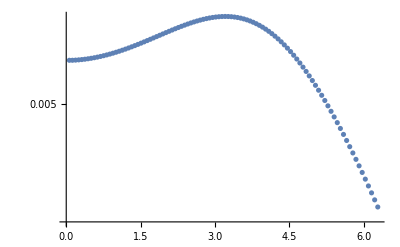
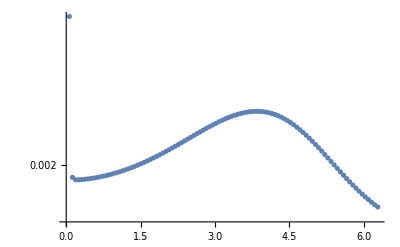
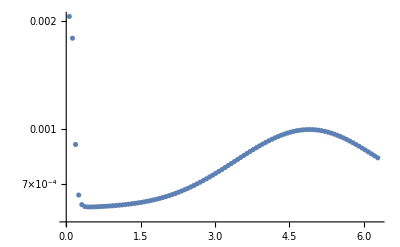
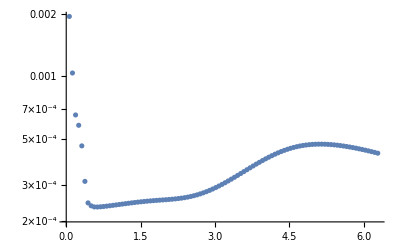
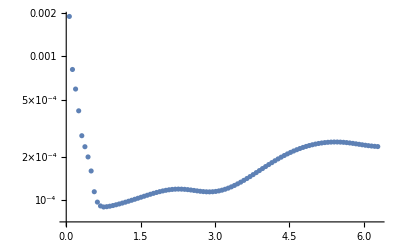
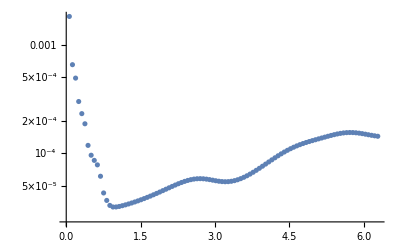
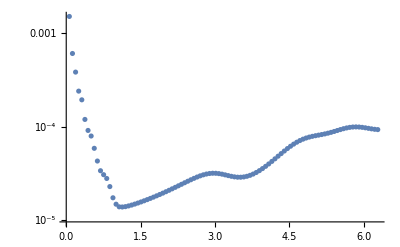
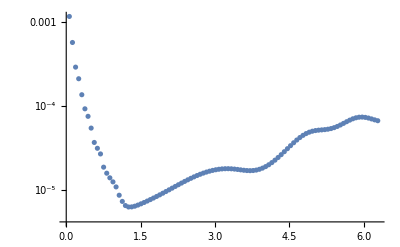

```mathematica
plotsRTE
plotsF
plots
```

## Data

```mathematica
If[!StringMatchQ[GraphType, "Chain"]&&!StringMatchQ[GraphType, "Ladder"], GraphType="Random"];
```

```mathematica
path=ToString[HamType]<>"-"<>ToString[GraphType]<>"-Nq="<>ToString[Nq]<>".dat";
CreateFile[path];
file=File[path];
```

```mathematica
Data={};
AppendTo[Data,"γ2ϵK:"];
Data=Join[Data,γ2ϵK];
AppendTo[Data,""];
Export[file,Data];
```